# Virtual Realizations of Quantum Computers

```mathematica
<<Q3`
<<WorkbookTools`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

## Hypothetical Spins

We will be denoting each qubit by the symbol S and accompanying indices .

```mathematica
Let[Qubit,S]
```

The Pauli operators are specified by the last index. For example, the Pauli operator S_j^x is denoted by S[j,1].

```mathematica
S[j,1]
```

S_j^x

```mathematica
S[j,1]**S[j,2]
S[j,1]**S[k,2]
```

ⅈ S_j^z

S_j^x S_k^y

## Spin-Boson Model

Denote the qubits by S and the cavity mode by a.

```mathematica
Let[Qubit,S]
Let[Boson,a]
```

This is the Hamiltonian.

```mathematica
opH=Dagger[a]**a+Ω S[3]/2+g(Dagger[a]+a)**S[1]
```

a^†a+g (a S^x+a^†S^x)+(Ω S^z)/2

Here is a truncated basis.

```mathematica
bs=Basis[{a,S}];
LogicalForm@bs
```

{0_a0_S,0_a1_S,1_a0_S,1_a1_S,2_a0_S,2_a1_S,3_a0_S,3_a1_S,4_a0_S,4_a1_S,5_a0_S,5_a1_S}

Here is the matrix representation of the Hamiltonian (showing only part of it), and the eigen-energies for a particular set of parameters.  The matrix representation is not exact as the basis has been truncated.

```mathematica
Ω=1;
g=1/10;
matH=Matrix[opH];
matH[[;;6,;;6]]//MatrixForm
val=N@Eigenvalues[matH]
```

(1/2 | 0 | 0 | 1/10 | 0 | 0
0 | -1/2 | 1/10 | 0 | 0 | 0
0 | 1/10 | 3/2 | 0 | 0 | 1/(5 √2)
1/10 | 0 | 0 | 1/2 | 1/(5 √2) | 0
0 | 0 | 0 | 1/(5 √2) | 5/2 | 0
0 | 0 | 1/(5 √2) | 0 | 0 | 3/2)

{5.52494,4.7328,4.2874,3.69409,3.29609,2.66746,2.32239,1.63601,1.35389,0.594847,-0.505013,0.395102}

Here you can see the (approximate) energy levels of the spin-boson model.

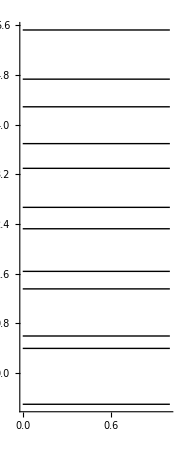

```mathematica
levels=Line@Thread@{Thread@{0,val},Thread@{1,val}};
Graphics[levels,
BaseStyle->Thick,
Axes->{None,True}]
```

## Dynamical Scheme

## Geometric/Topological Scheme

## Measurement-Based Scheme

Consider an arbitrary state that the first qubit can have.

```mathematica
vec=Ket[]c[0]+Ket[S[1]->1]c[1];
vec//LogicalForm
```

c_0 0_S_1+c_1 1_S_1

This shows the most elementary quantum circuit model that is used for a measurement-based quantum computation.

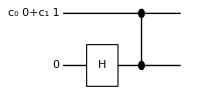

```mathematica
qc=QuissoCircuit[vec,LogicalForm[Ket[],S[2]],S[2,6],CZ[S[1],S[2]],"PortSize"->{2,0.5}]
```

Here is the result of the operations of the gates.

```mathematica
out=Elaborate[qc]
```

(c_0 ␣)/(√2)-(c_1 1_S_11_S_2)/(√2)+(c_1 1_S_1)/(√2)+(c_0 1_S_2)/(√2)

It is useful to rewrite the resulting state in the following form.

```mathematica
new=QuissoFactor[out,S[1]];
new//LogicalForm
```

0_S_1⊗((c_0 0_S_2)/(√2)+(c_0 1_S_2)/(√2))+1_S_1⊗((c_1 0_S_2)/(√2)-(c_1 1_S_2)/(√2))

Using the relation between the CNOT and CZ gate, the following is an equivalent quantum circuit model.

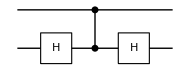
-Graphics-=-Graphics-

```mathematica
Row@{QuissoCircuit[CNOT[S[1],S[2]]],"=",QuissoCircuit[S[2,6],CZ[S[1],S[2]],S[2,6]]}
```

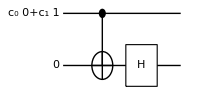

```mathematica
new=QuissoCircuit[vec,LogicalForm[Ket[],S[2]],CNOT[S[1],S[2]],S[2,6],"PortSize"->{2,0.5}]
```

```mathematica
Elaborate[qc]-Elaborate[new]
```

0

Consider a quantum circuit model of the following form.

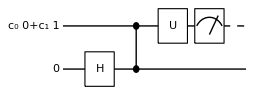

```mathematica
opU=Rotation[ϕ,S[1,1],"Label"->"U"];
qc=QuissoCircuit[vec,LogicalForm[Ket[],S[2]],S[2,6],CZ[S[1],S[2]],opU,Measurement[S[1]],"PortSize"->{2,0.5}]
```

```mathematica
out=Elaborate[qc];
QuissoFactor[out]//LogicalForm
```

Measurement::nonum: Cannot perform a measurement on a nonnumeric state vector. Probability half is assumed.

(c_0 Cos[ϕ/2] 0_S_2+c_0 Cos[ϕ/2] 1_S_2-ⅈ c_1 0_S_2 Sin[ϕ/2]+ⅈ c_1 1_S_2 Sin[ϕ/2])/(√2)

To make the structure of the resulting state, let us examine the state before the measurement. In addition, remove the expected Hadamard gate on the second qubit.

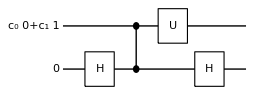

```mathematica
opU=Rotation[ϕ,S[1,1],"Label"->"U"];
qc=QuissoCircuit[vec,LogicalForm[Ket[],S[2]],S[2,6],CZ[S[1],S[2]],opU,S[2,6],"PortSize"->{2,0.5}]
```

```mathematica
out=Elaborate[qc];
QuissoFactor[out,S[1]]//LogicalForm
```

0_S_1⊗(c_0 Cos[ϕ/2] 0_S_2-ⅈ c_1 1_S_2 Sin[ϕ/2])+1_S_1⊗(c_1 Cos[ϕ/2] 1_S_2-ⅈ c_0 0_S_2 Sin[ϕ/2])